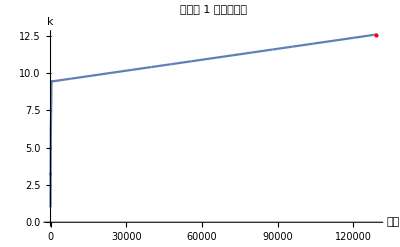

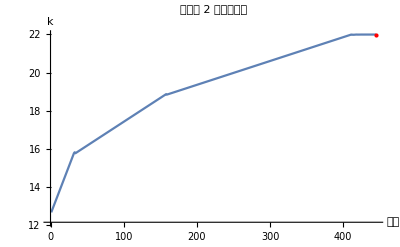

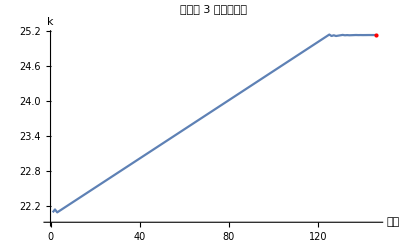

特征值（数值精度）：

{12.5664,21.9911,25.1325}

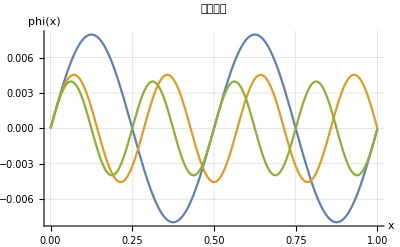

```mathematica
(*特征值求解函数*)shootEV[]:=Module[{tol=10^-8,m=3,kk,n,dk,x,phi,oldphi,dphi,evFun,sol,currentGuess,kHistory,eigenvalueMarkers,initialSearchSteps=50},(*定义微分方程*)evFun[x_,phi_]:={phi[[2]],-$k^2*phi[[1]]};
(*预分配特征值数组*)kk=ConstantArray[0.0,m];
eigenvalueMarkers={};(*用于存储特征值位置*)(*循环查找前'm'个特征值*)n=1;
currentGuess=1.0;(*从1.0开始搜索*)While[n≤m,(*---初始搜索阶段（更系统化）---*)kHistory={};
dk=0.1;(*初始搜索的较小且恒定的dk。*)oldphi=10^6;(*在内循环*之前*初始化oldphi*)While[True,AppendTo[kHistory,currentGuess];
sol=Quiet@Check[NDSolve[{y''[x]==-currentGuess^2*y[x],y[0]==0,y'[0]==0.1},y,{x,0,1},Method->"StiffnessSwitching"],$Failed,{NDSolve::ndsz,NDSolve::ndcf}];
If[sol===$Failed,phi={10^6,10^6};,phi=y/.sol[[1]];];
If[Head[phi]===InterpolatingFunction,dphi=phi[1];,dphi=10^6;];
If[dphi*oldphi<0,(*检测到符号变化！*)Break[];(*退出初始搜索循环*)];
(*oldphi=dphi;*)(*在初始搜索循环*内部*更新oldphi*)currentGuess+=dk;(*初始搜索的k增量。*)If[currentGuess>20,(*防止无限循环*)Print["警告：未找到符号变化。结果可能不完整。"];
Return[{$Failed,"警告：未找到符号变化。"}];(*修改为返回一个列表*)];];(*While True结束*)(*---二分法阶段（精炼）---*)dk=dk/2.0;(*减少二分法的步长*)While[Abs[dphi]>tol,currentGuess=currentGuess+dk;
AppendTo[kHistory,currentGuess];
sol=Quiet@Check[NDSolve[{y''[x]==-currentGuess^2*y[x],y[0]==0,y'[0]==0.1},y,{x,0,1},Method->"StiffnessSwitching"],$Failed,{NDSolve::ndsz,NDSolve::ndcf}];
If[sol===$Failed,phi={10^6,10^6};,phi=y/.sol[[1]];];
If[Head[phi]===InterpolatingFunction,dphi=phi[1];,dphi=10^6;];
If[dphi*oldphi<0,currentGuess=currentGuess-dk;
AppendTo[kHistory,currentGuess];
dk=dk/2.0;];
oldphi=dphi;];(*While Abs[dphi]>tol结束*)kk[[n]]=currentGuess;(*存储特征值*)AppendTo[eigenvalueMarkers,{currentGuess,0}];
(*绘制k历史*)Print[ListLinePlot[kHistory,AxesLabel->{"迭代","k"},PlotLabel->StringJoin["特征值 ",ToString[n]," 的搜索历史"],PlotRange->All,Epilog->{Red,PointSize[Large],Point[{Length[kHistory],currentGuess}]}]];
(*---准备下一个特征值搜索---*)currentGuess=kk[[n]]+0.1;(*正确的增量*)n++;(*在存储特征值后递增n*)];(*While[n≤m]结束*)(*---绘制组合特征函数---*)plot=Plot[Evaluate[Table[If[Head[y/.NDSolve[{y''[x]==-kk[[i]]^2*y[x],y[0]==0,y'[0]==0.1},y,{x,0,1},Method->"StiffnessSwitching"][[1]]]===InterpolatingFunction,(y/.NDSolve[{y''[x]==-kk[[i]]^2*y[x],y[0]==0,y'[0]==0.1},y,{x,0,1},Method->"StiffnessSwitching"][[1]])[x],Null],{i,1,m}]],{x,0,1},PlotRange->All,AxesLabel->{"x","phi(x)"},PlotLabel->"特征函数",GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8]]];
Return[{kk,plot}];(*返回一个列表*)];

(*调用函数并显示结果*)
{eigenvalues,plot}=shootEV[];

If[eigenvalues=!=$Failed,Print["特征值（数值精度）："];
Print[N[eigenvalues,16]];
Print[plot];,Print[plot];]
```